## Muonium Antimatter Gravity Interferometry Code

This code is used to calculate intensity distributions of a muonium beam that passes through 2 grating structures. Ana Soter’s version used a completely uniform grating structure. This has been modified to also account for a grating structure with 50 nm wide slits separated by distances that alternate around 50 nm according to an adjustable offset. A notebook containing more detailed notes about the construction of this grating structure can be found on the Google Drive: “New grating coefficients by Alyssa.nb”

```mathematica
(* Based on PhD thesis of McMorran *)

tbefore = TimeUsed[]; 

(* ShowFullPlot dictates whether or not the section Computing Intensity Along Z-Axis runs. Setting this to True will produce a intensity plot along the z-axis,ranging from the source beam with Initial Beam Parameters *)
  
ShowFullPlot = False; (* Set to True to show intensity along entire z range, False to just show at position of third grating*)

OriginalGrating = False; (* True to use Soter's uniform grating, false to use our grating coefficients with alternating separation between slits *)
(* adjust nonuniform grating structure *)
(*!!DO NOT set centeroffset more than + or - 25 nm!! slits will overlap and some of the open space will be double counted in calculation of fourier componenets so they will no longer be valid unless you manually change the limits of the sums *)

centeroffset = -15*10^(-9); (* use to adjust nonuniform grating (only used if OriginalGrating = False) offset of the center of the middle slit, -5*10^(-9) gives 5 nm to the left - we can adjust the severity of the imperfection here - 0 will give the same results as the uniform grating *)

(* INPUT PARAMETERS *)
(* The sections below–Beam parameters;Grating parameters–are noted in the IGOR Code for Modeling Grating Interferometers (ICfMGI) as "///// INPUT PARAMETERS – SI UNITS" but have been reordered/regrouped slightly to better demonstrate what the variables model: The Beam & Gratings *)

(* Initial Beam Parameters *)
(* The initial beam parameters are used to compute the mutual intensity function, and are, in order of appearance, 

1. Initial Beam Width
2. Initial Radius of Wavefront Curvature (Where r -> infinity approaches a planar wave)
3. Initial Coherence Width (Or: Transverse Coherence Width)
4. Wavelength (does not change. With Mu: 0.58*10^(-9)

and are all defined in McMorran's Thesis' Appendix A, Model for partial coherence and wavefront curvature in grating interferometers, Section II. Propogation of a GSM Beam Through a Two-Grating System, Subsection A. *)

w0=1*10^-3; (*initial beam width, adjust this to match x-ray aperture *)
r0= -999999999999999999999; (*initial radius of wavefront curvature *)
ell0= w0;(* initial transverse coherence width *)
lambda=  0.56*10^(-9)(*with Mu: 0.58*10^-9;*) 

(* Grating Parameters *)
(* The grating parameters are required to A) Properly model the grating structure in Fourier space and B) Determine the GSM parameters and resultant intensity functions after passing through a grating *)

d=1*10^-7; (*period of grating used if OriginalGrating = True *)
LT= d^2/lambda; (*Talbot length*)
NZ = Floor[20*10^-3/LT];
nu1=.5; (*grating 1 open fraction *)
nu2=.5; (*grating 2 open fraction *)
Z1=5*10^-3 ; (* position of grating 1, 5 mm along z axis *)
Z2=Z1+0.05 (*Z1+NZ*LT;*) (* position of grating 2, you can adjust the spacing between the gratings here, currently 5 cm to match x-ray *)
Z3 = Z2+(Z2-Z1); (* position of grating 3, all are equally spaced *)
X2=0;  (*initial offset of G2*)
theta=0;(*twist between gratings, in degrees*)

(* Limits of the plot, noted as //// SPATIAL LIMITS OF SIMULATION in the ICfMGI *)

Zmin= 1*10^-3;(*1*10^-3;*)
Zmax= Z3+ 0.5*Z1;(*1*10^-3;*) (*the full plot goes slightly beyond the position of the third grating*)
Xmin=-4*10^(-3);(*-5000*d*) (*-400*d*) (* min and max x values of the plot, adjust these to zoom in/out *)
Xmax=4*10^(-3)(*5000*d*) (*1900*d*)

xpoints=500;(*resolution in the x direction*)
zpoints=500;(*resolution in the z direction*)

dZ=(Zmax-Zmin)/zpoints;(*step resolution used in computation*)
dX=(Xmax-Xmin)/xpoints;(*step resolution used in computation*)

image = True;(*switch to turn on or off the effects of image charges on an electron beam*)

xticks = {{1,Zmin},{1+0.2*(Zmax-Zmin)/dZ,Zmin+0.2*(Zmax-Zmin)},{1+0.4*(Zmax-Zmin)/dZ,Zmin+0.4*(Zmax-Zmin)}, {1+0.6*(Zmax-Zmin)/dZ,Zmin+0.6*(Zmax-Zmin)} , {1+0.8*(Zmax-Zmin)/dZ,Zmin+0.8*(Zmax-Zmin)},{1+(Zmax-Zmin)/dZ,Zmax}} ;
(*yticks = {{1,Xmin},{1+0.25*(Xmax-Xmin)/dX,Xmin+0.25*(Xmax-Xmin)},{1+0.5*(Xmax-Xmin)/dX,Xmin+0.5*(Xmax-Xmin)},{1+0.75*(Xmax-Xmin)/dX,Xmin+0.75*(Xmax-Xmin)},  {1+(Xmax-Xmin)/dX,Xmax}} ;*)
yticks = {{1,Xmin},{1+0.25*(Xmax-Xmin)/dX,Xmin+0.25*(Xmax-Xmin)},{1+0.5*(Xmax-Xmin)/dX,Xmin+0.5*(Xmax-Xmin)},{1+0.75*(Xmax-Xmin)/dX,Xmin+0.75*(Xmax-Xmin)},  {1+(Xmax-Xmin)/dX,Xmax}} ; (* these are used for the final plot, where the Z values are graphed on the x axis and the X values are on the y axis*)
```

5.6×10^-10

0.055

1/250

### Grating Fourier Components This section, as was done with the ICfMGI, “Computes the Fourier components describing a diffraction grating, including phase grating effects due to Coulomb interactions between the electron wave function and inner surfaces of the grating Soter’s Uniform Grating

(-20 | -2.91989×10^-16
-19 | -0.0451105
-18 | 0.0137662
-17 | -0.0313134
-16 | -7.52731×10^-17
-15 | 0.00928826
-14 | -0.0883968
-13 | 0.000315647
-12 | -2.69784×10^-16
-11 | -0.0217123
-10 | 0.0646567
-9 | -0.0720902
-8 | -4.55191×10^-17
-7 | 0.127709
-6 | -0.00488389
-5 | 0.15419
-4 | -2.30371×10^-16
-3 | -0.127277
-2 | 0.504597
-1 | -0.0493853
0 | 1.
1 | -0.0493853
2 | 0.504597
3 | -0.127277
4 | -2.30371×10^-16
5 | 0.15419
6 | -0.00488389
7 | 0.127709
8 | -4.55191×10^-17
9 | -0.0720902
10 | 0.0646567
11 | -0.0217123
12 | -2.69784×10^-16
13 | 0.000315647
14 | -0.0883968
15 | 0.00928826
16 | -7.52731×10^-17
17 | -0.0313134
18 | 0.0137662
19 | -0.0451105
20 | -2.91989×10^-16)

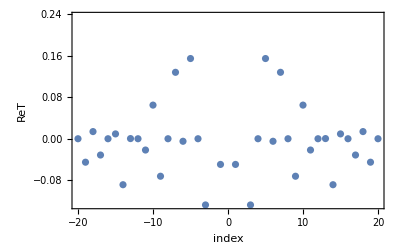

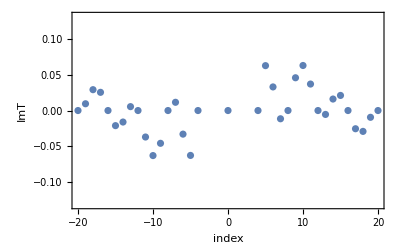

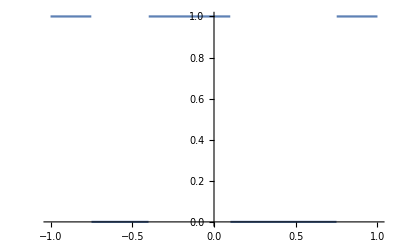

```mathematica
If[OriginalGrating,{
(*defining grating parameters*)
width=nu2*d; (* width given by open fraction of grating 2 times the period of the grating, total open width of a single slit*)
thick=0;
(* thick represents the physical thickness of the grating, s.t.thick=0 represents a perfectly thin grating,ignoring the effects of beam diffraction within the grating. *)

wedgeangle=0; (* as defined in McMorran's thesis,wedgeangle is the angle from one side of the grating to the other (through the holes in the grating. The holes aren't cut/etched straight through but on an angle) - this value is to be given in degrees, as seen by the deg to rad conversion when defining alpha later in the code *)

tilt=0; (* tilt (or, when converted to radians, beta) is the angle between the gratings if one is rotated in the xy plane - see FIG 1 of Appendix A of McMorran's thesis,  included below, where tilt would represent phi, and is defined as theta in the ICfMGI *)
-Graphics-
ReT=Transpose[{-20+(#-1)&/@Range[41],ConstantArray[0,41]}]; (* this constructs an array of paired values, (# between -20 and 20  (index n in the fourier series), 0s (to be filled in with the real components of the fourier series of the grating)) right now each value is (n, 0)*)
ImT=ReT; (* same as above to be used for imaginary components*)

res=1000; (* res used to compute fourier components, number of terms in the sum for each nth component *)
nu=width/d; (* this gives back nu2 *)

alpha=wedgeangle*Pi/180; (* conversion from degrees to radians for the wedgeange *)
beta=tilt*Pi/180; (*converts tilt angle to radians*)

(*setting minimum and maximum position of x that the fourier components are summed over, depends on if beta is positive or negative and the relationship between alpha (wedgeangle) and beta (tilt), represents the open width of a single slit *)
minposX=If[beta≥0,-((width Cos[beta])/2)+width/res,If[Abs[beta]≤alpha,-((width Cos[beta])/2)+width/res,-((width Cos[beta])/2)+width/res-thick*(Tan[alpha]-Tan[beta])]];
maxposX=If[beta≥0,If[beta≤alpha,(width Cos[beta])/2-width/res,(width Cos[beta])/2-width/res+thick*(Tan[alpha]-Tan[beta])],(width Cos[beta])/2-width/res];

x2pnt[arr__,n_]:=Position[arr[[All,1]],n][[1]][[1]];(*this is a function that is used to return index where n occurs in the index of ImT or ReT*)

Do[
(* this constructs the components of a fourier series, ReT holds cos terms of the fourier series from n = -20 to 20 and ImT holds the sin terms, used in gp1 and gp2,  *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

(* n from -20 to 20 and ex, which increments x from minposX to (maxposX - 1 increment) by increments of width/res*)
{n,-20,20,1},
{ex,minposX,maxposX-width/res, width/res}]},
(* Based on PhD thesis of McMorran *)

tbefore = TimeUsed[]; 

(* Toggle full plot on or off and swicth between grating structures *)
ShowFullPlot = False; (* Set to True to show intensity along entire z range, False to just show at final position*)
OriginalGrating = False; (* True to use Soter's uniform grating, false to use our grating coefficients with alternating separation between slits *)

(* adjust nonuniform grating structure *)
(*!!DO NOT set centeroffset more than + or - 25 nm!! slits will overlap and some of the open space will be double counted in calculation of fourier componenets so they will no longer be valid unless you manually change the limits of the sums *)
centeroffset = -15*10^(-9); (* use to adjust nonuniform grating (only used if OriginalGrating = False) offset of the center of the middle slit, -5*10^(-9) gives 5 nm to the left - we can adjust the severity of the imperfection here - 0 will give the same results as the uniform grating *)

(* Beam parameters *)

w0=1*10^-3; (*initial beam width, adjust this to match x-ray aperture *)
r0= -999999999999999999999; (*initial radius of wavefront curvature *)
ell0= w0;(* initial transverse coherence width *)
lambda=  0.56*10^(-9)(*with Mu: 0.58*10^-9;*) 

(* Grating parameters *)

d=1*10^-7; (*period of grating used if OriginalGrating = True *)
LT= d^2/lambda; (*Talbot length*)
NZ = Floor[20*10^-3/LT];
nu1=.5; (*grating 1 open fraction *)
nu2=.5; (*grating 2 open fraction *)
Z1=5*10^-3 ; (* position of grating 1, 5 mm along z axis *)
Z2=Z1+0.05 (*Z1+NZ*LT;*) (* position of grating 2, you can adjust the spacing between the gratings here, currently 5 cm to match x-ray *)
Z3 = Z2+(Z2-Z1); (* position of grating 3, all are equally spaced *)
X2=0;  (*initial offset of G2*)
theta=0;(*twist between gratings, in degrees*)

(* Limits of the plot *)

Zmin= 1*10^-3;(*1*10^-3;*)
Zmax= Z3+ 0.5*Z1;(*1*10^-3;*) (*the full plot goes slightly beyond the position of the third grating*)
Xmin=-4*10^(-3);(*-5000*d*) (*-400*d*) (* min and max x values of the plot, adjust these to zoom in/out *)
Xmax=4*10^(-3)(*5000*d*) (*1900*d*)

xpoints=500;(*resolution in the x direction*)
zpoints=500;(*resolution in the z direction*)

dZ=(Zmax-Zmin)/zpoints;(*step resolution used in computation*)
dX=(Xmax-Xmin)/xpoints;(*step resolution used in computation*)

image = True;(*switch to turn on or off the effects of image charges on an electron beam*)

xticks = {{1,Zmin},{1+0.2*(Zmax-Zmin)/dZ,Zmin+0.2*(Zmax-Zmin)},{1+0.4*(Zmax-Zmin)/dZ,Zmin+0.4*(Zmax-Zmin)}, {1+0.6*(Zmax-Zmin)/dZ,Zmin+0.6*(Zmax-Zmin)} , {1+0.8*(Zmax-Zmin)/dZ,Zmin+0.8*(Zmax-Zmin)},{1+(Zmax-Zmin)/dZ,Zmax}} ;
(*yticks = {{1,Xmin},{1+0.25*(Xmax-Xmin)/dX,Xmin+0.25*(Xmax-Xmin)},{1+0.5*(Xmax-Xmin)/dX,Xmin+0.5*(Xmax-Xmin)},{1+0.75*(Xmax-Xmin)/dX,Xmin+0.75*(Xmax-Xmin)},  {1+(Xmax-Xmin)/dX,Xmax}} ;*)
yticks = {{1,Xmin},{1+0.25*(Xmax-Xmin)/dX,Xmin+0.25*(Xmax-Xmin)},{1+0.5*(Xmax-Xmin)/dX,Xmin+0.5*(Xmax-Xmin)},{1+0.75*(Xmax-Xmin)/dX,Xmin+0.75*(Xmax-Xmin)},  {1+(Xmax-Xmin)/dX,Xmax}} ; (* these are used for the final plot, where the Z values are graphed on the x axis and the X values are on the y axis*)



(* our grating coefficients. An overview/tutorial of how these were constructed can be found in "New grating coefficients by Alyssa.nb" on the drive *)


{
ReT=Transpose[{-20+(#-1)&/@Range[41],ConstantArray[0,41]}]; (* ReT matrix holds the real components of the Fourier coefficients for n values from -20 to 20, not yet filled it*)
ImT = ReT; (*Same as above for the imaginary components*)
res=1000;(* number of terms summed to find the coefficients *)
d = 200*10^(-9); (* new period is 200 nm *)
nu = 0.5; (* open fraction, 50% of grating is open *)
width = nu*d; (* open fraction times period gives open width in a period, this now gives double the width of a slit/the total width of two slits *)

minposcenterslit = -25*10^(-9) + centeroffset; (* left edge of slit (at -25 nm for uniform grating) is shifted by centeroffset*) 
maxposcenterslit = 25*10^(-9) + centeroffset; (* right egde of slit shifted by centeroffset from 25 nm *)

(*locations of edges of slits, start and end points for sums *)
(*first half slit*)
minslit1 = -100*10^(-9);
maxslit1 = -75*10^(-9);
(*middle/full slit*)
minslit2 = minposcenterslit;
maxslit2 = maxposcenterslit;
(*third slit, half*)
minslit3 = 75*10^(-9);
maxslit3 = 100*10^(-9);

x2pnt[arr__,n_]:=Position[arr[[All,1]],n][[1]][[1]];(*this is a function that is used to return index where n occurs in the index of ImT or ReT*)

increment = width/res; 

(* we're breaking up the Do loop into separate sums, one for each slit *)
Do[
(* this does the sum for the first slit *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit1,maxslit1-increment, increment}];

Do[
(* now add the second slit *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit2,maxslit2-increment, increment}];

Do[
(* and the third *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit3,maxslit3-increment, increment}];


SlitRepresentation = Piecewise[{{1,x> minslit1&&x<maxslit1},{0, x<minslit2 && x>maxslit1},{1, x<maxslit2 && x>minslit2},{0, x>maxslit2 && x<minslit3},{1, x>minslit3 && x<maxslit3}},0]; (*Piecewise function used to graph a visual representation of slits*)
}];

(* each of the fourier terms in each array are divided by res *) 
 ReT[[All,2]]/=res;
ImT[[All,2]]/=res; 

MatrixForm[ReT]

ListPlot[ReT,Frame->True,FrameLabel->{"index","ReT"}]
ListPlot[ImT,Frame->True,FrameLabel->{"index","ImT"}]

If[Not[OriginalGrating],Plot[SlitRepresentation, {x, minslit1, maxslit3}]]
```

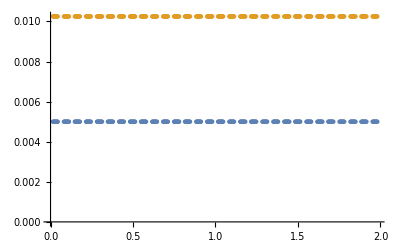

```mathematica
(* izx and ix are created here, but not yet filled with intensity values. ix will give paired values of intensity vs position in x at a particular value of z, izx stores ix for each different position z *)
izx=ConstantArray[ConstantArray[0,zpoints],xpoints];(* this is an array of 500 arrays of 500 zeros, 500 slices in the z axis of 500 intensity profiles in x (or y) *)
fmap=ConstantArray[ConstantArray[0,zpoints],Ceiling[xpoints/2]];(* the same as above, but only 250 in x (half the resolution)*)
ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}]; (* a list of ordered pairs (x, 0) from xmin incremented to xmax *)
g1=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(2 xpoints-1))&/@Range[xpoints*2],ConstantArray[NaN,xpoints*2]}];(* (x, NaN) but the resolution is doubled so there's twice as many entries as above *)
g2=g1; (* g2 is another array equal to g1 *)
vis=Transpose[{(Zmin-Z1)+(#-1) ((Zmax-Zmin)/(zpoints-1))&/@Range[zpoints],ConstantArray[0,zpoints]}]; (* (z, 0) pairs same as (x, 0) pairs, ordered pairs over z range *)

f1[x_]:=If[((x>d*Round[x/d]-d*nu1/2)&&(x<d*Round[x/d]+d*nu1/2)),NaN,Z1]; (* this is a function, gives NaN if input is within d*nu1/2 of the closest int to x/d and Z1 otherwise *)
If[Z1≥Zmin && Z1≤Zmax,g1[[All,2]]=Map[f1,g1[[All,1]]]]; (* if Z1 is between Zmin and Zmax, function f1 is applied to x values in g1 and then the result is put in the second index *)
f2[x_]:=If[((x-X2>d*Round[x/d]-d*nu2/2)&&(x-X2<d*Round[x/d]+d*nu2/2)),NaN,Z2]; (* function, gives NaN if value - X2 is within a range and Z2 if out of it, similar to f1 but includes an offset *)
If[Z2≥Zmin && Z2 ≤ Zmax,g2[[All,2]]=Map[f2,g2[[All,1]]]]; (* applies f2 to g2 if Z2 is within the range *)
ListPlot[{g1,g2}] (* this should show Z1 and Z2 for a specific range of x values *)
```

### Calculating The GSM Parameters at Grating 1 (First Grating) It can be seen that the first function seen below -- which is Equation 6 from Appendix A of McMorran’s Thesis -- is a function of 4 variables, these being: 1. z_ = Distance of wavefront curvature from the origin 2. rθ = Radius of Curvature for the wavefront 3. ellθ = The initial coherence width (or transverse coherence length) 4. wθ = The initial beam width The objective of these functions is to first utilize the paraxial approximation to Zernike’s general propagation law for fields with coherence properties, as seen in the Appendix of Appendix A of McMorran’s Thesis, and incorporate them into the already-adjusted mutual intensity function for isotropic beams. So, the following three equations: (1) wz[z_,r0_,ell0_,w0_]:=w0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)] (2) ellz[z_,r0_,ell0_,w0_]:=ell0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)] (3) rz[z_,r0_,ell0_,w0_]:=z/(1-zp[z,r0]/(z*(1+lambda^2*zp[z,r0]^2/(ell0^2*w0^2)))) are seen in the paper as: -Graphics- where Equation (1) is the function to calculate the Beam Width, Equation (2) calculates the Coherence Length, and Equation (3) calculates the Radius of Wavefront Curvature. The table below shows the language translation between McMorran’s thesis, the IGOR Pro 6.0 Code, and this notebook, with respect to the equations and variables found in this section, Calculating the GSM Parameter at Grating 1. It should be noted that in this notebook, wz and w0 are used to indicate the variable w (beam width) at a specific z value and the initial value, respectively. This holds true for all variables being used in Calculating the GSM Parameter at Grating 1. Variable | Name in Thesis | Name in IGOR | Name in Mathematica Distance of wavefront curvature from origin | z | z | z GSM Radius of wavefront curvature | r | v | r GSM coherence width | l | el | ell GSM beam width | w | w | w

```mathematica
zp[z_,v_]:= (v z)/(v+z);
(*Magnification factor due to wavefront curvature –used to simplify the three functions below. 
This can be found in the IGOR Pro code noted as //compute magnification factor due to wavefront curvature *)

wz[z_,r0_,ell0_,w0_]:=w0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)];(*function to calculate GSM beam width*)

ellz[z_,r0_,ell0_,w0_]:=ell0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)];(*GSM coherence length*)

rz[z_,r0_,ell0_,w0_]:=z/(1-zp[z,r0]/(z*(1+lambda^2*zp[z,r0]^2/(ell0^2*w0^2))));(*radius of wavefront curvature*)
(* applies the functions above at Z1 calculated from the initial values for the beam parameters *)

r1=rz[Z1,r0,ell0,w0];
ell1=ellz[Z1,r0,ell0,w0];
w1=wz[Z1,r0,ell0,w0];
```

Power::infy: Infinite expression 1/0. encountered.

### Grating Function 0 The functions in this section are used, as noted in the IGOR Pro 6.0 Code, to “//get intensity profile after no grating” and are coded in the following manner: function gp0(z01,r0,el0,w0) variable z01,r0,el0,w0 variable w1 wave ix gp0 w1 = w(z01,r0,el0,w0) ix = exp(-pi*(x/w1)^2) end So, the following three equations: (1) wz[z_,r0_,ell0_,w0_]:=w0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)] (2) ellz[z_,r0_,ell0_,w0_]:=ell0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)] (3) rz[z_,r0_,ell0_,w0_]:=z/(1-zp[z,r0]/(z*(1+lambda^2*zp[z,r0]^2/(ell0^2*w0^2)))) are seen in the paper as: -Graphics- where Equation (1) is the function to calculate the Beam Width, Equation (2) calculates the Coherence Length, and Equation (3) calculates the Radius of Wavefront Curvature. The table below shows the language translation between McMorran’s thesis, the IGOR Pro 6.0 Code, and this notebook, with respect to the equations and variables found in this section, Calculating the GSM Parameter at Grating 1. It should be noted that in this notebook, wz and w0 are used to indicate the variable w (beam width) at a specific z value and the initial value, respectively. This holds true for all variables being used in Calculating the GSM Parameter at Grating 1. Variable | Name in Thesis | Name in IGOR | Name in Mathematica Distance of wavefront curvature from origin | z | z | z GSM Radius of wavefront curvature | r | v | r GSM coherence width | l | el | ell GSM beam width | w | w | w

General::munfl: Exp[-812.327] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1268.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1826.52] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

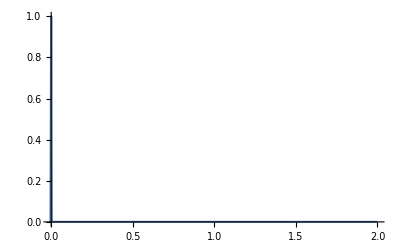

```mathematica
(* This function calculates the beam spreading as it propogates, without any effects from a grating structure, ie. prior to the first grating *)
(* calculates w1 (beam width at given values for z, r, ell, an inital w), creates a blank ix matrix (giving intensity at specific x values), with intensity given by e^(-Pi*(x/w1)^2) (should be equal to 1 (max) at x = 0) in the second index for each pair in ix - each pair is (x, intensity at x) *)
gp0[z01_,r0_,ell0_,w0_]:=Block[
{w1=wz[z01,r0,ell0,w0],
ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}]
},

ix[[All,2]]=Map[Exp[-Pi*(#/w1)^2]&,ix[[All,1]]];

Return[ix];
];
(* applies the function gp0 at location Zmin + dZ*50 (50 steps away from Zmin) *)
gp0[Zmin+dZ*50,r0,ell0,w0];
ListPlot[%, PlotRange->All, Joined->True]
```

### Grating function 1 The functions in this section are a reproduction of what is noted as the process to “//get intensity profile after one grating” in the ICfMGI and are guided by Appendix A, Section II, Subsection B. GSM after transmission through one grating

```mathematica
(* this is similar to gp0 but models the beam after it passes through the first grating. The exact formula can be found in McMorran's thesis, Appendix A (look for the mutual intensity functions) *)
gp1[z12_,r1_,ell1_,w1_]:=Block[
{ell2=ellz[z12,r1,ell1,w1],(* beam parameters *)
w2=wz[z12,r1,ell1,w1],
r2=rz[z12,r1,ell1,w1],
ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}],
cutoff=1*10^-3, (* cutoff used to round small values to 0 *)
lim=4, (* uses coefficents up to + and - limit for n and m. As n and m increase, coefficients are multiplied by a decreasing exponential so it is not necessary to cover the full range *)
dn=0,dm=0,coef=1},

Do[
dn=n-m;
dm=(m+n)/2;

(* ignoring the image charge defines coefficients using the sinc function, if not uses coefficients from ReT and ImT *)
If[ Not[image],(*If true, ignore effect of image charge*)
coef=Sinc[nu1*Pi*n]*Sinc[nu1*Pi*m]*nu1^2,coef=ReT[[x2pnt[ReT,n]]][[2]]*ReT[[x2pnt[ReT,m]]][[2]]+ImT[[x2pnt[ReT,n]]][[2]]*ImT[[x2pnt[ReT,m]]][[2]]];

coef*=Exp[-Pi*(dn*lambda*z12/(d*ell2))^2]; (* multiplies coefficients by an exponential *)

If[coef≥cutoff,ix[[All,2]]+=Map[(coef*Exp[-Pi*((#-dm*lambda*z12/d)/w2)^2]*Cos[2*Pi*(dn/d)*(#-dm*lambda*z12/d)*(1-z12/r2)])&,ix[[All,1]]];
], (* multiplies terms with coefficients larger than the cutoff by another exponential and sums them to compute intensity at each x value *)

{n,-lim,lim,1},{m,-lim,lim,1}]; (* increments n and m by one between + and - limit *)
Return[ix];
];
```

```mathematica
gp1[Z1+LT,r1,ell1,w1]; (* calculates intensity as a function of x (ix) at LT (Talbot length) beyond the first grating. You can see it spread out if you increase the distance away *)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

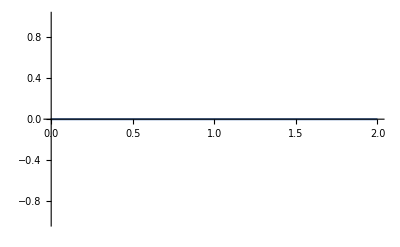

```mathematica
ListPlot[%,Joined->True, PlotRange->All]
```

### Grating function 2 This is similar to Grating Function 1, however, to calculate this, the code seen below is gp1 applied onto itself, or rather, applied onto the model gp1 produces right before the second grating. This is seen in Appendix A as Equation 17. The functions included in this section, however, are those described as Equations 18(a – e) and can account for the twist between gratings, as defined in the prelude section of this notebook as theta, and is seen as mytheta in the function. Additionally, it should be noted that zXY, such as z12 represents the distance between two gratings, X and Y.

```mathematica
gp2[z12_,z23_,mytheta_,ell1x_,w1x_,r1x_,ell1y_,w1y_,r1y_,X2_]:=Block[
{theta=Pi*mytheta/180,
d1=d,
d2=d,

z13=z12+z23,
ell3x=ellz[z12+z23,r1x,ell1x,w1x],
w3x= wz[z12+z23,r1x,ell1x,w1x],
r3x=rz[z12+z23,r1x,ell1x,w1x],

ell3y=ellz[z12+z23,r1y,ell1y,w1y],
w3y=wz[z12+z23,r1y,ell1y,w1y],
r3y=rz[z12+z23,r1y,ell1y,w1y],

ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}],
phix=ix,phi=0,(*phix is empty but takes the same form as ix for phi as a function of x. Phi will be calculated and phix will be filled in at each x*)
cutoff=1*10^-3, 
lim=4,
coef=1,dn=0,dm=0,m=0,n=0,a=0,b=0,c=0,d=0}, 

Do[
dn=n1-n2; 
n=(n1+n2)/2;
dm=m1-m2;
m=(m1+m2)/2;
a = x2pnt[ReT,m1]; (*a, b, c and d are used to match the indices with their locations in ReT and ImT *)
b=x2pnt[ReT,m2];
c=x2pnt[ReT,n1];
d=x2pnt[ReT,n2];


If[Not[image],(*If true, ignore effect of image charge*)
{coef=Sinc[nu1*Pi*m1]+0ⅈ,
coef*=Sinc[nu1*Pi*m2+0ⅈ]},
{coef=ReT[[a]][[2]]+ImT[[a]][[2]]ⅈ,(* full/complex form of coefficients given by adding the real and imaginary part *)
coef*=ReT[[b]][[2]]-ImT[[b]][[2]]ⅈ}]; (* multiply coefficients of m1 * coefficients of m2 *)

coef*=ReT[[c]][[2]]+ImT[[c]][[2]]ⅈ; (* same as before for n1 and n2 *)
coef*=ReT[[d]][[2]]-ImT[[d]][[2]]ⅈ;

(*Accounting for twist dependence of visibility*) 
coef*=Exp[-Pi*(dn*Sin[theta]*lambda*z23/(d2*ell3y))^2];
coef*=Exp[-Pi*(lambda*z23*(dn*Cos[theta]+dm*z13/z23)/(d1*ell3x))^2];


(*Print[ix[[All,1]]];
ix[[All,2]]+=Map[(Re[coef]*Cos[#[[2]]]-Im[coef]*Sin[#[[2]]])*Exp[-Pi*((#[[1]]-(lambda*z23/d1)*(n*Cos[theta]+m*z13/z23))/w3x)^2]&,phi];
Print[ix]*)
If[Re[coef]≥cutoff ||Im[coef]≥cutoff,(* Re[coef]/Im[coef] return the real/imaginary part of the calculated coefficients, calculates phix here and uses it in calculation of ix  *)
{
phi=dn*n*(1-z23/r3x)*Cos[theta]^2+dn*n*(1-z23/r3y)*Sin[theta]^2+dn*m*(1-z13/r3x)*Cos[theta];phi+=dm*n*(1-z13/r3x)*Cos[theta]+dm*m*(z13/z23)*(1-z13/r3x);phi*=2*Pi*lambda*z23/(d1^2);phi-=2*Pi*dn*X2/d2;phix[[All,2]]=Map[(phi-(2*Pi*#/d2)*(dn*Cos[theta]*(1-z23/r3x)+dm*(1-z13/r3x))&),phix[[All,1]]];

ix[[All,2]]+=Map[(Re[coef]*Cos[#[[2]]]-Im[coef]*Sin[#[[2]]])*Exp[-Pi*((#[[1]]-(lambda*z23/d1)*(n*Cos[theta]+m*z13/z23))/w3x)^2]&,phix]
}
]
,

{m1,-lim,lim,1},{m2,-lim,lim,1},{n1,-lim,lim,1},{n2,-lim,lim,1}];

Return[ix]];
```

#### Testing:

```mathematica
gp2[Z2-Z1,Zmin+200*dZ,theta,ell1,w1,r1,ell1,w1,r1,X2]; (* intensity at Zmin + 200*dZ beyond the second grating *)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot[%,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Compute intensity at the position of 3rd grating:
```

If ShowFullPlot = False, these are the final results/ graphs

This is effectively calculating Equation 17 of Appendix A, which is the intensity distribution just before the second grating, but instead, for just before, or rather, at, the position of the 3rd grating, since no gp3 acts on the intensity distribution produced by gp2.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{500,2}

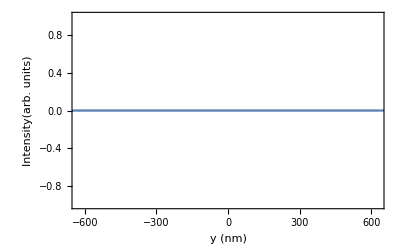

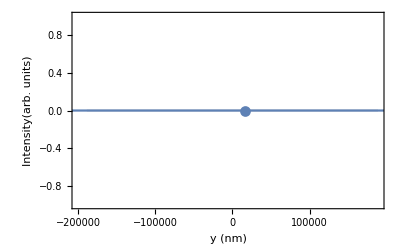

gp2 Min, Max, Contrast=

0

0

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

Divide::indet: Indeterminate expression 0/0 encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Indeterminate

-Graphics-

```mathematica
gp2dat=gp2[Z2-Z1,Z2-Z1,theta,ell1,w1,r1,ell1,w1,r1,X2]; (* intensity at distance beyond Z2 equal to spacing between gratings - at grating 3 *)
gp2dat[[All,1]]*=10^9; (* multiplies all x values by 10^9 (conversion from m to nm for plotting) *)
Dimensions[gp2dat] (* gives size of gp2dat*)
gp2min=Min[gp2dat[[All,2]]]; (*min intensity*)
gp2max=Max[gp2dat[[All,2]]]; (*max intensity*)
gp2mean=(gp2max+gp2min)/2; (*mean intensity*)
gp2amp=gp2max-gp2mean; (*amplitude of intensity*)
bb:=Style[#,{Bold, Larger,Black}]&; (* function, just applies a style for a graph *)
marker=Graphics[]; (*also for graphing*)
gp2dat;
Show[Plot[gp2mean+gp2amp*Sin[2* π*x/100+ π/2],{x,-200 π,200 π}(* this part is background to show diff between min and max intensity*),PlotStyle->LightGray,Frame->True,AxesOrigin->{-602,0.2}(*this is a really small portion of it, idk why*),FrameLabel->{bb@" y (nm)",bb@"Intensity(arb. units)"},TargetUnits->{1*10^-9,}],ListPlot[gp2dat,PlotMarkers->{"•",11},Joined->True] (*dots show gp2dat*)
]
(*Print["gp2 Min, Max=",MinMax[gp2dat[[All,2]]]];*)
Show[Plot[gp2mean+gp2amp*Sin[2* π*x/10000+ π/2],{x,-60000 π,60000 π (* change plot range in here *)}(* plotting again over bigger range to show the whole thing, mess with these parameters to change the sin function background *),PlotStyle->LightGray,Frame->True,AxesOrigin->{-200000,0.2} (* mess with this to change where the graph starts*),FrameLabel->{bb@" y (nm)",bb@"Intensity(arb. units)"},TargetUnits->{1*10^-9,}],ListPlot[gp2dat,PlotMarkers->{"•",11},Joined->True, PlotRange->All] (*dots show gp2dat*)
]
Text["gp2 Min, Max, Contrast="]
gp2min
gp2max
(gp2max-gp2min)/(gp2max+gp2min)

gp2dat[[All, 1]]*= 1*10^(-6); (* conversion from nm to mm *)
gp2dat[[All, 2]]/= gp2max ;(* normalization so that maximum intensity is always 1 *)
gp2max=Max[gp2dat[[All,2]]]
Show[ListPlot[gp2dat,Joined->True, PlotRange->{0,1.1}, Frame->True, FrameLabel->{bb@" y (mm)",bb@"Intensity"}]]
```

### Computing Intensity Along Z-Axis The computation seen below is noted in Appendix L of Electron Diffraction and Interferometry Using Nanostructures as // MAIN LOOP - compute intensity profile at each step along optical axis In McMorran’s thesis, it first defines the location along the z axis as a function of the initial z position and the step resolution in the computation To better understand the differences between the code and this notebook, a table translating each term has been included below – it should be reminded that the fringe profile is the intensity distribution Variable | Name in IGOR | Name in Mathematica Minimum z-axis position of beam | zstart | zmin Resolution along z-axis | zres | zpts Position of fringe profile along z-axis | zloc | zpos Looking at the defining of variables, constants, and some functions at the beginning of this notebook, it can be seen that the values remain the same for the first and last variables in the table above, but the resolution along the z-axis has changed from 300 to 500 So below, what will be produced is the intensity distribution along the x-axis at a number of z positions, this number equal to the resolution along the z-axis, or as defined in this notebook, zpts, a collection of points equally spaced between zmin, the initial beam position, and zmax, the maximum z-axis position of the beam being modelled, slightly past the third grating, as can be seen in the graph produced by this section.

```mathematica
(* Calculation of Intensity Function at Each Step Along z-Axis *)
If[ShowFullPlot,{

Do[
zpos=Zmin+i*dZ;
If[zpos>Z2,
ix=gp2[Z2-Z1,zpos-Z2,theta,ell1,w1,r1,ell1,w1,r1,X2]
,
If[zpos>Z1,
ix=gp1[zpos-Z1,r1,ell1,w1]
,
ix=gp0[zpos,r0,ell0,w0]
]
];
filter1[x_]:=If[x<0,0.,x];
The line above seems to be a mistranslation from the initial ICfMGI, which eliminated the negative values for intensity. However, this eliminates the negative x values instead

ix[[All,2]]=Map[filter1,ix[[All,2]]];
(*ix[[All,2]]=Map[filter2,ix[[All,2]]];*)
ix[[All,2]]/=Max[ix[[All,2]]];
izx[[All,i+1]]=ix[[All,2]];
,
{i,0,zpoints-1,1}]

}];
```

```mathematica
(*Plotting of Intensity Function at Each Step Along z-Axis*)
If[ShowFullPlot, {

Axis Scale Adjustment
ticx = 0.1*10^-3;
ticz =  4*10^-3;
scalex = 10^-3;
scalez = 10^-3;

General Plot Parameter Adjustment
ListDensityPlot[ 
{izx}, ColorFunction->ColorData["SunsetColors"]  , AspectRatio->0.75,ImageSize->1200,PlotRange->All,PlotRangePadding->.001, FrameLabel->{Switch[scalez,LT ,"Z distance [Talbot length]",1,"Z distance [m]",  10^-3, "Z distance [mm]",10^-6 ,"Z distance [um]", 10^-9,"Z distance [nm]"],
Switch[scalex,d,"Y distance [slit spacing]",1,"Y distance [m]",  10^-3, "Ydistance [mm]",10^-6 ,"Y distance [um]", 10^-9,"Y distance [nm]"]},LabelStyle->(FontSize->12),
FrameTicks->{{{#,Round[(Xmin+#*dX)/scalex,0.0001] }&/@Range[0,xpoints,ticx/dX],None},{{#,NumberForm@((Zmin+#*dZ)/scalez)}&/@Range[0,zpoints,ticz/dZ],None}}]}]
```

#### Time used:

```mathematica
tafter=TimeUsed[]; (*calculating how long this part takes*)
Seconds = (tafter-tbefore); (* time in seconds *)
Minutes =(tafter-tbefore)/60; (*in minutes*)
Text["Time in seconds:"] 
Seconds
Text["Time in minutes:"] 
Minutes
```

Time in seconds:

3.96096

Time in minutes:

0.066016